## Random data from simulation

```mathematica
(* Import CSV file *)
alldata=Import[NotebookDirectory[]~~"Simulated_data_2021-07-27-14-59-41.csv"];
(* Extract data from CSV file.  z = redshifts; error = ±z;  nangledata = RA & Dec, converted to unit vector;  distmoddata = distance modulus *)
zdata=alldata[[All,1]];
errordata=alldata[[All,3]];
nangledata=alldata[[All,{4,5,6}]];
distmoddata=alldata[[All,2]];
```

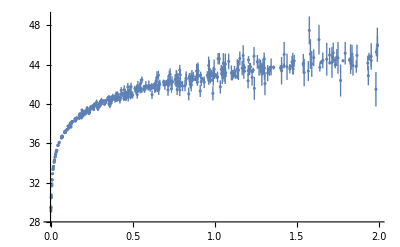

```mathematica
ListPlot[Transpose[{zdata,Thread[PlusMinus[distmoddata,errordata]]}]]
```

## Defining cosmological solution, constants, & constraints

```mathematica
(*Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];*)
zmax=2.; (*Trigger value to stop integration of background solution *)

(* Numerically solve ODEs for cosmic expansion. *)
ABvacmetric0=ParametricNDSolveValue[
{ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk+ⅇ^(-3 AA0[τ]) Ωm+ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+BB0'[τ]^2==0,ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk-1/3 ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+2 AA0'[τ] BB0'[τ]-BB0'[τ]^2-(2 AA0''[τ])/3+(2 BB0''[τ])/3==0,
WhenEvent[AA0'[τ]+2BB0'[τ]==0, Sow[True]; "StopIntegration"],(* Set flag to "True" & stop if we get to a contracting phase *)
WhenEvent[Min[Exp[-(AA0[τ]+2BB0[τ])],Exp[-(AA0[τ]-BB0[τ])]]>zmax+1+0.1,"StopIntegration"],
(* Stop if we get to z = zmax in all directions without entering a contracting phase *)
AA0[0]==BB0[0]==AA0'[0]-1==BB0'[0]-b0==0},{AA0,BB0},{τ,-∞,0},{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0},Method->{"ParametricSensitivity"->None}]
c=299724.58 (* in km/s *)
paramconstraints=And[ΩB≥0,Ωm≥0,Ωr≥0]
```

ParametricFunction[<>]

299725.

ΩB≥0&&Ωm≥0&&Ωr≥0

## Calculate χ^2 for data & parameters

```mathematica
initdirection=Normalize[RandomVariate[NormalDistribution[],3]]
currentpt={0.01,0.01,0.28,0.01,0.69,0,0.7,initdirection}
 (* Our Universe, more or less *)

cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->currentpt[[1;;6]]];
{{currentA,currentB},contractflag}=ABvacmetric0@(Sequence@@Take[currentpt,6])//Reap;
contractflag=Or@@Append[Flatten[contractflag],False];
If[contractflag, Print["Warning!  This universe has a contracting phase."]]

DcurrentA=Derivative[1][currentA];
DcurrentB=Derivative[1][currentB];
bbtime=currentA["Domain"][[1,1]];

cθmin=10^-6;
helperα=2; 

helpersoln=NDSolve[{
D[qo[z,cθ],z]==((DcurrentA[te[z,cθ]]+2DcurrentB[te[z,cθ]])Exp[-6 currentB[te[z,cθ]]] cθ^2+(DcurrentA[te[z,cθ]]-DcurrentB[te[z,cθ]])(1-cθ^2))^-1 UnitStep[te[z,cθ]-bbtime],
(* The above expression is called 𝒬 in my notes of 2021-07-07 *)
D[te[z,cθ],z]==-Exp[2currentA[te[z,cθ]]-2currentB[te[z,cθ]]] (1+z)D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
D[υo[z,cθ],z]==(1-υo[z,cθ])^(helperα+1)Exp[-2currentA[te[z,cθ]]-4currentB[te[z,cθ]]] (1+z)^-2 D[qo[z,cθ],z]UnitStep[te[z,cθ]-bbtime],
qo[0,cθ]==te[0,cθ]==υo[0,cθ]==0},{qo,υo,te},{z,0,2},{cθ,cθmin,1},Method->{"Adams","PDEDiscretization"->{"MethodOfLines"}}];
distmod[z_,nvec_,paramlist_,bbtime_]:=Module[{cosparams=paramlist[[1;;6]],h=paramlist[[7]],n0vec=paramlist[[8]],cθ,teval,qoval,ψoval,υoval},
cosparamrules=Thread[{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0}->cosparams];
cθ=nvec.n0vec;
{teval,qoval,υoval}={te[z,Abs[cθ]],qo[z,Abs[cθ]],υo[z,Abs[cθ]]}/.First[helpersoln];
teval=Max[teval,bbtime];
ψoval=Max[1/helperα(1/(1-υoval)^helperα-1),0];
(*qoval=qo[cθ][z];
ψoval=ψo[cθ][z];*)
-2.5 Log10[(Exp[2currentA[teval]+10currentB[teval]](h*10^-3/c)^2/((cθ^2+Exp[6currentB[teval]](1-cθ^2))^(5/2)qoval ψoval Re[Sinc[qoval √(-3 Ωk(1-cθ^2))]]))/.cosparamrules]
];
χsq[params_]:=∑_(i=1)^Length[zdata] (distmoddata[[i]]-distmod[zdata[[i]],nangledata[[i]],params,bbtime])^2/(errordata[[i]])^2;
{t1, b1} = AbsoluteTiming[currentchisq=χsq[currentpt]]; t1 (* initial chi-squared value *)

distmod[zdata[[1]], nangledata[[1]], currentpt, bbtime]

dataList = {{"redshifts", "teval", "qoval", "psioval"}};
cθ = .25;
For[z = 0.025, z < 2.1, z = z+.025,
{teval,qoval,υoval}={te[z,Abs[cθ]],qo[z,Abs[cθ]],υo[z,Abs[cθ]]}/.First[helpersoln];
ψoval=Max[1/helperα(1/(1-υoval)^helperα-1),0];
AppendTo[dataList, {z, teval, qoval,ψoval }];];
Export["mathematicaData.csv", dataList]
```

{0.0701736,0.996995,-0.0328143}

{0.01,0.01,0.28,0.01,0.69,0,0.7,{0.0701736,0.996995,-0.0328143}}

ParametricNDSolveValue::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

0.0579512

41.583

InterpolatingFunction::dmval: Input value {2.025,0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

mathematicaData.csv